```mathematica
X = {0., 0.2, 0.4, 0.6, 0.8};
```

```mathematica
Y ={0.8, 0.85, 0.825, 0.9, 0.5};
```

```mathematica
j=Table[i,{i,0,4}];
```

```mathematica
n = 5;
```

```mathematica
G=(-1)^(n-j)*t*Product[(t-i),{i,1,n}]/(Factorial[j]*Factorial[n-j]*(t-j));
```

```mathematica
F[t]= G.Y;
```

```mathematica
L = F[t]/.t->x/0.2;
```

```mathematica
polymonial = Expand[L]
```

0.8+1.66667 x-11.7188 x^2+27.0833 x^3-19.5312 x^4

```mathematica
XY = {{0., 0.8}, {0.2, 0.85}, {0.4, 0.825},{0.6, 0.9},{0.8, 0.5}};
```

```mathematica
yp[z_]=InterpolatingPolynomial[XY, z]
```

0.5+(-0.8+z) (-0.375+(-1.09375+(-0.260417-19.5313 (-0.2+z)) (-0.4+z)) (0.+z))

```mathematica
Expand[yp[z]]
```

0.8+1.66667 z-11.7188 z^2+27.0833 z^3-19.5313 z^4

```mathematica
rd[ta_,n_]:=Sum[ta[[i,2]]*Product[If[j≠i,(ta[[i,1]]−ta[[j,1]]),1],{j,1,n}],{i,1,n}];
```

```mathematica
New[ta_,n_,x_]:=Sum[rd[ta,k]*Product[(x−ta[[i,1]]),{i,1,k−1}],{k,1,n}];
```

```mathematica
q = New[XY, Length[XY], x]
```

0.8+0.01 (0.+x)+0.096 (-0.2+x) (0.+x)+0.0052 (-0.4+x) (-0.2+x) (0.+x)+0.0384 (-0.6+x) (-0.4+x) (-0.2+x) (0.+x)

```mathematica
Expand[q]
```

0.8-0.0106272 x+0.109776 x^2-0.04088 x^3+0.0384 x^4

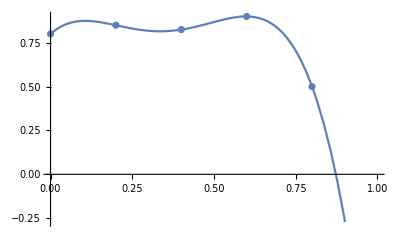

```mathematica
Show[Plot[polymonial, {x, 0, 1}], ListPlot[XY]]
```

```mathematica
f[X1] = X1-2*Cos[X1];
```

```mathematica
X1 = {1, 1.2, 1.4, 1.6, 1.8, 2., 2.2};
```

```mathematica
Y1 = N[f]
```

{-2.,-1.76013,-1.44212,-1.05067,-0.593413,-0.0806046,0.475284}

```mathematica
X1Y1 = Table[{X1[[i]],Y1[[i]]}, {i, 1, 6}]
```

{{1,-2.},{1.2,-1.76013},{1.4,-1.44212},{1.6,-1.05067},{1.8,-0.593413},{2.,-0.0806046}}

```mathematica
polymonial2 = InterpolatingPolynomial[X1Y1, s];
```

```mathematica
polymonial2=Expand[polymonial2]
```

-2.10579-0.575985 s+0.353379 s^2+0.452186 s^3-0.131714 s^4+0.00792409 s^5

```mathematica
s = {1, 1.2, 1.4, 1.6, 1.8, 2., 2.2};
```

```mathematica
polymonial2
```

{-2.,-1.76013,-1.44212,-1.05067,-0.593413,-0.0806046,0.47518}

```mathematica
polymonial2-Y1
```

{0.,0.,-4.44089×10^-16,0.,-4.44089×10^-16,-4.44089×10^-16,-0.000104591}

```mathematica
Max[Abs[polymonial2-Y1]]
```

0.000104591

```mathematica
polgr = Expand[InterpolatingPolynomial[X1Y1, o]]
```

-2.10579-0.575985 o+0.353379 o^2+0.452186 o^3-0.131714 o^4+0.00792409 o^5

```mathematica
Clear[y]
y[a_]:= a - 2Cos[a];
X1 = {1, 1.2, 1.4, 1.6, 1.8, 2., 2.2};
xy1 = Table[{i, y[i]}, {i , 1, 2.2, 0.2}]
```

{{1.,-0.0806046},{1.2,0.475284},{1.4,1.06007},{1.6,1.6584},{1.8,2.2544},{2.,2.83229},{2.2,3.377}}

```mathematica
Clear[x]
```

```mathematica
pl = Expand[InterpolatingPolynomial[xy1, x]]
```

-2.00813+1.03776 x+0.92612 x^2+0.078677 x^3-0.13216 x^4+0.0172096 x^5-0.0000803025 x^6

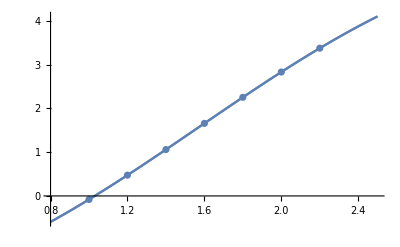

```mathematica
Show[Plot[pl, {x, 0.8,2.5}], ListPlot[xy1], Plot[y[a], {a, 0.8, 2.5}]]
```

```mathematica
Plot[y[a], {a, 0.8, 2.5}, PlotStyle -> {{Thick,Red}}]
```

-Graphics-

```mathematica
n=6;
```

```mathematica
Do[e[i]=-Cos[Pi*(2*i+1)/(2*n+2)],{i, 1,n}]
```

```mathematica
b= 1;
a = 2.2;
```

```mathematica
Do[newNode[i]=N[(b+a)/2 + y[i]*(b-a)/2],{i,1,n}]
```

```mathematica
TA = Table[newNode[i],{i,n}]
```

{1.64836,-0.0993762,-1.38799,-1.58437,-1.05961,-0.847796}

```mathematica
K = x - 2*Cos[x];
```

```mathematica
x = TA;
```

```mathematica
Y2 = N[K]
```

{1.80334,-2.08951,-1.75157,-1.55722,-2.03804,-2.17107}

```mathematica
xY2 = Table[{TA[[i]], Y2[[i]]}, {i, 1,6}]
```

{{1.64836,1.80334},{-0.0993762,-2.08951},{-1.38799,-1.75157},{-1.58437,-1.55722},{-1.05961,-2.03804},{-0.847796,-2.17107}}

```mathematica
Clear[z]
```

```mathematica
Chebpolynom = Expand[InterpolatingPolynomial[xY2, z]]
```

-1.99925+1.0097 z+1.0239 z^2+0.0186874 z^3-0.0850441 z^4-0.00818816 z^5

```mathematica
Clear[y];
```

```mathematica
Chebpolynom
```

{1.80334,-2.08951,-1.75157,-1.55722,-2.03804,-2.17107}

```mathematica
Y2
```

{1.80334,-2.08951,-1.75157,-1.55722,-2.03804,-2.17107}

```mathematica
Clear[x]
```

```mathematica
Clear[z]
```

```mathematica
pl = Expand[InterpolatingPolynomial[xy1, z]]
```

-2.00813+1.03776 z+0.92612 z^2+0.078677 z^3-0.13216 z^4+0.0172096 z^5-0.0000803025 z^6

```mathematica
x = TA;
```

```mathematica
pl
```

{1.80334,-2.10221,-2.45448,-2.64633,-2.35125,-2.34608}

```mathematica
Chebpolynom
```

{1.80334,-2.08951,-1.75157,-1.55722,-2.03804,-2.17107}

```mathematica
Clear[y]
```

```mathematica
y[a_]:= a - 2Cos[a];
```

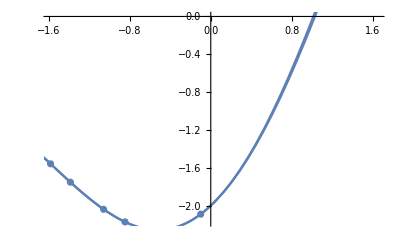

```mathematica
Show[ListPlot[xY2], Plot[Chebpolynom, {z, -2,2}], Plot[y[a], {a, -2, 2}]]
```